```mathematica
DR[n_,g_,K_]:=(1+g)/(1+g n/K)
```

```mathematica
smax=0.3
```

0.3

```mathematica
lambda=10
```

10

```mathematica
sel[t_]:=smax Sin[2π t/lambda]
```

```mathematica
(*Deterministic Simulation, constant carrying capacity, symm W *)
Kf0=Kr0=1000;
bf=0; br =0;
n0=20;
r=0.5;
a1=0.5; (* for allele A *)
a2 =0.5; (* for allele a *)
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj1={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[tt=0,tt<ncyc lambda,tt++;
Kpf=Kf0 Exp[bf Sin[2π tt/lambda]];
Kpr=Kr0 Exp[br Sin[2π tt/lambda]];
nA1a=nA1 Exp[a1 sel[tt]];
na1a=na1 Exp[-a2 sel[tt]];
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj1=Append[Ntraj1,{La,LA}]
]
```

g= 0.02

g= 0.2

g= 2

g= 20

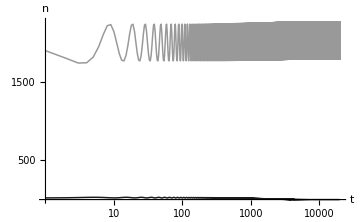

```mathematica
g11=ListPlot[Ntraj1[[1]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

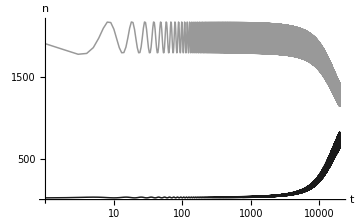

```mathematica
g12=ListPlot[Ntraj1[[2]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

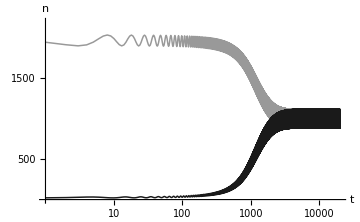

```mathematica
g13=ListPlot[Ntraj1[[3]],Joined->True, PlotRange->{0,2200},PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

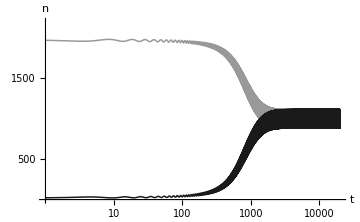

```mathematica
g14=ListPlot[Ntraj1[[4]],Joined->True, PlotRange->{0,2200}, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

```mathematica
(*Deterministic Simulation, constant carrying capacity, WA > Wa*)
Kf0=Kr0=1000;
bf=0; br =0;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=1;
a2 =0;
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj2={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 Exp[a1 sel[t]];
na1a=na1 Exp[-a2 sel[t]];
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj2=Append[Ntraj2,{La,LA}]
]
```

g= 0.02

g= 0.2

g= 2

g= 20

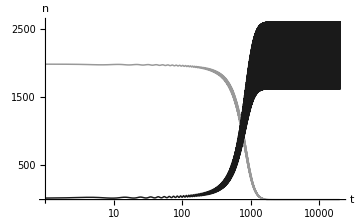

```mathematica
g21=ListPlot[Ntraj2[[1]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

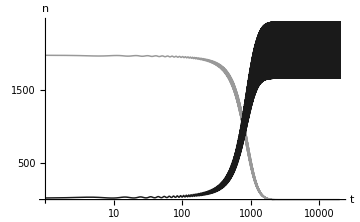

```mathematica
g22=ListPlot[Ntraj2[[2]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

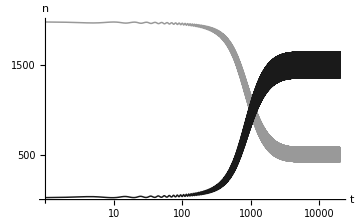

```mathematica
g23=ListPlot[Ntraj2[[3]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

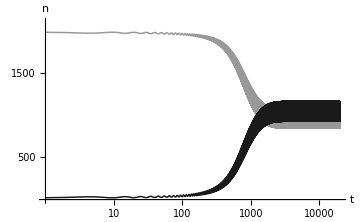

```mathematica
g24=ListPlot[Ntraj2[[4]],Joined->True,PlotRange->{0,2100}, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

```mathematica
(*Deterministic Simulation, constant carrying capacity, WA < Wa *)
Kf0=Kr0=1000;
bf=0; br =0;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=0;
a2 =1;
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj3={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 Exp[a1 sel[t]];
na1a=na1 Exp[-a2 sel[t]];
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj3=Append[Ntraj3,{La,LA}]
]
```

g= 0.02

g= 0.2

g= 2

g= 20

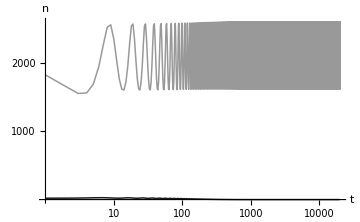

```mathematica
g31=ListPlot[Ntraj3[[1]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{1000,2000,3000,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

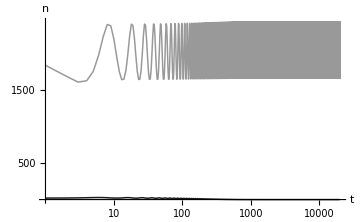

```mathematica
g32=ListPlot[Ntraj3[[2]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

```mathematica
PlotRange->{0,2100},
```

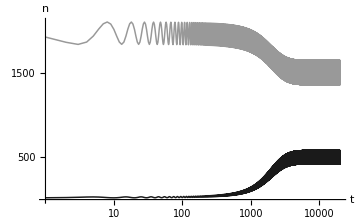

```mathematica
g33=ListPlot[Ntraj3[[3]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

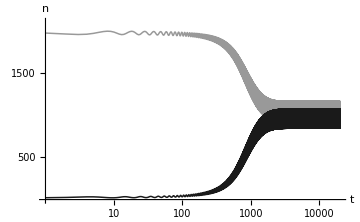

```mathematica
g34=ListPlot[Ntraj3[[4]],Joined->True,PlotRange->{0,2100}, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

```mathematica
(*Deterministic Simulation, cyclic carrying capacity, A in phase,  WA = Wa *)
Kf0=Kr0=1000;
bf=0.5; br =0;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=0.5;
a2 =0.5;
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj4={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 Exp[a1 sel[t]];
na1a=na1 Exp[-a2 sel[t]];
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj4=Append[Ntraj4,{La,LA}]
]
```

g= 0.02

g= 0.2

g= 2

g= 20

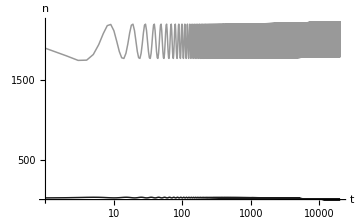

```mathematica
g41=ListPlot[Ntraj4[[1]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

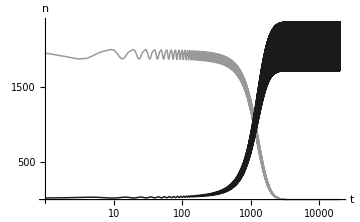

```mathematica
g42=ListPlot[Ntraj4[[2]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

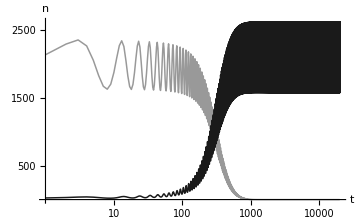

```mathematica
g43=ListPlot[Ntraj4[[3]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

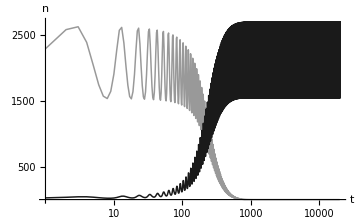

```mathematica
g44=ListPlot[Ntraj4[[4]],Joined->True, PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

```mathematica
(*Deterministic Simulation, cyclic carrying capacity, A in phase, WA > Wa *)
Kf0=Kr0=1000;
bf=0.5; br =0;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=1;
a2 =0;
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj5={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 Exp[a1 sel[t]];
na1a=na1 Exp[-a2 sel[t]];
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj5=Append[Ntraj5,{La,LA}]
]
```

g= 0.02

g= 0.2

g= 2

g= 20

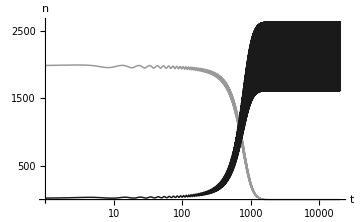

```mathematica
g51=ListPlot[Ntraj5[[1]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500, 2000,2500, 3000,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

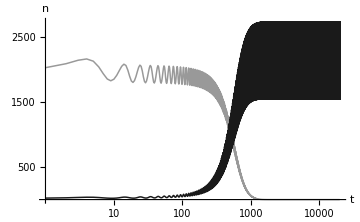

```mathematica
g52=ListPlot[Ntraj5[[2]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

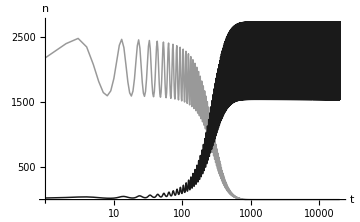

```mathematica
g53=ListPlot[Ntraj5[[3]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

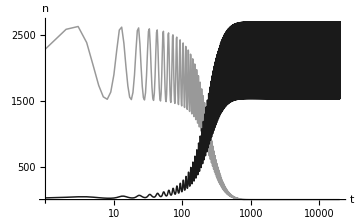

```mathematica
g54=ListPlot[Ntraj5[[4]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

```mathematica
(*Deterministic Simulation, cyclic carrying capacity, A in phase, WA < Wa *)
Kf0=Kr0=1000;
bf=0.5; br =0;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=0;
a2 =1;
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj6={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 Exp[a1 sel[t]];
na1a=na1 Exp[-a2 sel[t]];
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj6=Append[Ntraj6,{La,LA}]
]
```

g= 0.02

g= 0.2

g= 2

g= 20

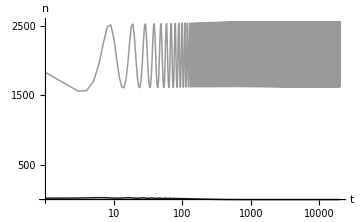

```mathematica
g61=ListPlot[Ntraj6[[1]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

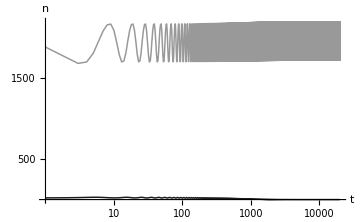

```mathematica
g62=ListPlot[Ntraj6[[2]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

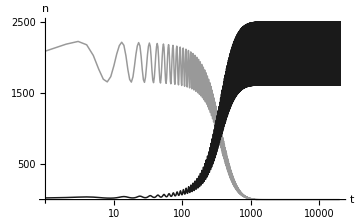

```mathematica
g63=ListPlot[Ntraj6[[3]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

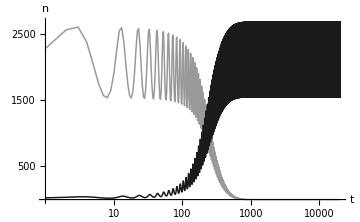

```mathematica
g64=ListPlot[Ntraj6[[4]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

```mathematica
(*Deterministic Simulation, cyclic carrying capacity, A not in phase, WA > Wa *)
Kf0=Kr0=1000;
bf=0.5; br =0;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=-1;
a2 =0;
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj7={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 Exp[a1 sel[t]];
na1a=na1 Exp[-a2 sel[t]];
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj7=Append[Ntraj7,{La,LA}]
];
```

g= 0.02

g= 0.2

g= 2

g= 20

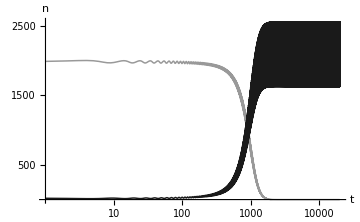

```mathematica
g71=ListPlot[Ntraj7[[1]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

```mathematica
g72=ListPlot[Ntraj7[[2]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
g73=ListPlot[Ntraj7[[3]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
g74=ListPlot[Ntraj7[[4]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
(* 11 const carrying capacity, AMF, WA > Wa*)
Kf0=Kr0=1000;
bf=0; br =0;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=1;
a2 =0;
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj11={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 (1+ a1 sel[t]);
na1a=na1 (1-a2 sel[t]);
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj11=Append[Ntraj11,{La,LA}]
]
```

g= 0.02

g= 0.2

g= 2

g= 20

```mathematica
g11a=ListPlot[Ntraj11[[1]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
g11b=ListPlot[Ntraj11[[2]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
g11c=ListPlot[Ntraj11[[3]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
g11d=ListPlot[Ntraj11[[4]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
(* 12 cyclic carrying capacity, AMF, WA > Wa *)
Kf0=Kr0=1000;
bf=0.5; br =0;
smax=0.3;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=1;
a2 =0;
gseries={2};
gr=0;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj12={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 (1+ a1 sel[t]);
na1a=na1 (1-a2 sel[t]);
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj12=Append[Ntraj12,{La,LA}]
]
```

g= 2

```mathematica
g12A=ListPlot[Ntraj12[[1]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
(* 12 cyclic carrying capacity, AMF, WA > Wa *)
Kf0=Kr0=1000;
bf=0.5; br =0;
smax=0.3;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=1;
a2 =0;
gseries={2};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj12B={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 (1+ a1 sel[t]);
na1a=na1 (1-a2 sel[t]);
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj12B=Append[Ntraj12B,{La,LA}]
]
```

g= 2

```mathematica
g12B=ListPlot[Ntraj12B[[1]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
(* 13 cyclic carrying capacity, AMF, WA > Wa, smax=0.2 *)
Kf0=Kr0=1000;
bf=0.5; br =0;
smax=0.2;
n0=20;
(*g=1.1;
rseries={ 0.2, 0.5, 0.8};*)
r=0.5;
a1=1;
a2 =0;
gseries={0.02,0.2,2,20};
gr=2;
ncyc=2000;
rep=Length[gseries];  (* g or r *)
Ftraj={};
Ntraj13={};
For[i=0,i<rep,i++;
g=gseries[[i]];(* g or r *)
Print["g= ", g];(* g or r *)
Traj={};
nA1=(1-r)n0;
na1=Kf0-nA1;
nA2=r n0;
na2 = Kr0-nA2;
For[t=0,t<ncyc lambda,t++;
Kpf=Kf0 Exp[bf Sin[2π t/lambda]];
Kpr=Kr0 Exp[br Sin[2π t/lambda]];
nA1a=nA1 (1+ a1 sel[t]);
na1a=na1 (1-a2 sel[t]);
nA1b=nA1a DR[nA1a+na1a,g,Kpf];
na1b=na1a DR[nA1a+na1a,g,Kpf];
nA2a=nA2 ;
na2a=na2 ;
nA2b=nA2a DR[nA2a+na2a,gr,Kpr];
na2b=na2a DR[nA2a+na2a,gr,Kpr];
nA1 = (1-r)(nA1b+ nA2b);
na1 = (1-r)(na1b+na2b);
nA2 =r (nA1b+nA2b);
na2 = r (na1b+na2b);
Traj=Append[Traj,{nA1+nA2,na1+na2,nA1+nA2+na1+na2}];
];
LA=Table[{Log[10,i],Traj[[i,1]]},{i,1,ncyc lambda}];
La=Table[{Log[10,i],Traj[[i,2]]},{i,1,ncyc lambda}];
Ntraj13=Append[Ntraj13,{La,LA}]
]
```

g= 0.02

g= 0.2

g= 2

g= 20

```mathematica
g13a=ListPlot[Ntraj13[[1]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
g13b=ListPlot[Ntraj13[[2]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
g13c=ListPlot[Ntraj13[[3]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-

```mathematica
g13d=ListPlot[Ntraj13[[4]],Joined->True,PlotStyle->{{Thickness[0.003],GrayLevel[0.6]},{Thickness[0.003], GrayLevel[0.1]}},Ticks->{{{1,"10"},{2,"100"},{3,"1000"},{4,"10000"}},{500,1000,1500,2000,2500,3000,3500,4000}}, AxesLabel->{Style["  t",Italic,20],Style["n",Italic,20]}, AxesStyle->18,ImageSize->Medium]
```

-Graphics-